{{0,0.2292},{8,0.137},{16,0.0337},{24,-0.0749},{32,-0.1756},{40,-0.2592}}

{{0,1.1361},{8,0.6437},{16,0.1609},{24,-0.3186},{32,-0.8016},{40,-1.2912}}

{0.0606932+0.0000131731 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.0000131731 | 1.71868×10^-6 | 7.66465 | 9.79163×10^-6
b | 0.0606932 | 0.000200246 | 303.092 | 6.33077×10^-23}

{-0.0387665+0.00130992 x, | Estimate | Standard Error | t-Statistic | P-Value
a | 0.00130992 | 0.0000398687 | 32.8558 | 8.03121×10^-10
b | -0.0387665 | 0.00217001 | -17.8647 | 9.87488×10^-8}

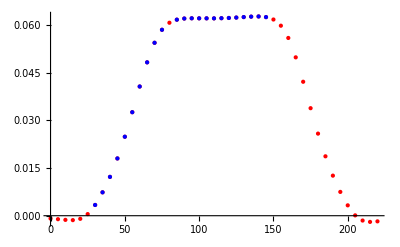

```mathematica
Clear[Sub, Filename, Filepath, rawData, partitionedData, gradientData, UnitsToMM, ArrayUnitsToMM, current, Lv, Lvc];
current = 0;
Filename = "m3-quad-"<>ToString[current]<>"A"; 
Filepath = StringJoin[NotebookDirectory[], "../data/"]; 

rawData = Import[StringJoin[Filepath, Filename, ".txt"], "Table"]; 

partitionedData = Partition[SortBy[Drop[rawData, 2], #1[[1]] + 100*#1[[2]] & ], 45];


randfeld = Map[{(#1[[1]]-1)*8, #1[[2]]}&, partitionedData[[All, 9, {2,3}]]]
nlmPlateau = NonlinearModelFit[randfeld, a*x + b, {a, b}, x]
plateaufeld = Map[{(#1[[1]]-1)*8, #1[[2]]}&, partitionedData[[All, 17, {2,3}]]]
nlmPlateau = NonlinearModelFit[plateaufeld, a*x + b, {a, b}, x]

Sub[n_] := partitionedData[[n]] - partitionedData[[n + 1]]; 

ArrayUnitsToMM[a_, b_] := (UnitsToMM[#1, b] & ) /@ a; 
UnitsToMM[a_, b_] := {b*(a[[1]] - 1), a[[2]]}; 

gradientData = ReplacePart[(Sub[#1] & ) /@ Range[5], {i_, j_, 1} -> j][[All,All,{1, 3}]]; 
gradientData = (ArrayUnitsToMM[#1, 5] & ) /@ gradientData;


xGradientData = (gradientData[[All,#1]] & ) /@ Range[45];
xGradientDataT = Transpose[xGradientData];

gmax= Map[Last,Flatten[Take[xGradientData, {18,30}],1]];
gmax={Mean[gmax], StandardDeviation[gmax]};

gV = Map[Integrate[Interpolation[#, InterpolationOrder -> 1][x], {x, 0, 220}]&,xGradientDataT];
gV = {Mean[gV], StandardDeviation[gV]};

Lvc={current, gV[[1]]/gmax[[1]], Sqrt[(gV[[2]]/gmax[[1]])^2+(gmax[[2]]*gV[[1]]/gmax[[1]]^2)^2]};
gmax={current, gmax[[1]], gmax[[2]]};


xGradientData = ({#1[[1]][[1]], (1/8)*Mean[#1[[All,2]]], (1/8)*StandardDeviation[#1[[All,2]]]} & ) /@ xGradientData; 
{Min[xGradientData[[All,2]]], Max[xGradientData[[All,2]]]};


path = StringJoin[Filepath, "parsed/", "m3-quad", "-MagneticLengths", ".txt"];
Lv = Import[path, "Table"];
Lv = ReplacePart[Lv, current/2+1 -> Lvc];
Lv = Map[{#[[1]], Round[#[[2]], 0.1], Round[#[[3]], 0.1]}&,Lv];
{Mean[Lv[[All,2]]], Sqrt[Last[FoldList[#1+#2^2&,0,Lv[[All,3]]]]]/Length[Lv]};
Export[path, Lv, "Table"];

path = StringJoin[Filepath, "parsed/", "m3-quad", "-CurrentGradient", ".txt"];
g = Import[path, "Table"];
g = ReplacePart[g, current/2+1 -> gmax];
g = Map[{#[[1]], Round[#[[2]], 0.1], Round[#[[3]], 0.1]}&,g];
Export[path, g, "Table"];

path2= StringJoin[Filepath, "parsed/", "m3-quad", "-example-r", ".txt"];
Export[path2, randfeld, "Table"];
path2= StringJoin[Filepath, "parsed/", "m3-quad", "-example-p", ".txt"];
Export[path2, plateaufeld, "Table"];


path = StringJoin[Filepath, "parsed/", Filename, "-MeanGradients", ".txt"]; 
Export[path, xGradientData, "Table"]; 


xOnlyGradient = ({#1[[1]], #1[[2]]} & ) /@ xGradientData;

GradientPlateau = Take[xOnlyGradient, {18, 30}]; 
GradientEdge = Take[xOnlyGradient, {7, 16}]; 

nlmPlateau = NonlinearModelFit[GradientPlateau, a*x + b, {a, b}, x]; 
nlmEdge = NonlinearModelFit[GradientEdge, a*x + b, {a, b}, x]; 
nlmPlateau[{"BestFit", "ParameterTable"}]
nlmEdge[{"BestFit", "ParameterTable"}]

Show[ListPlot[xOnlyGradient, PlotStyle -> Red], ListPlot[GradientEdge, PlotStyle -> Blue], ListPlot[GradientPlateau, PlotStyle -> Blue]]
```